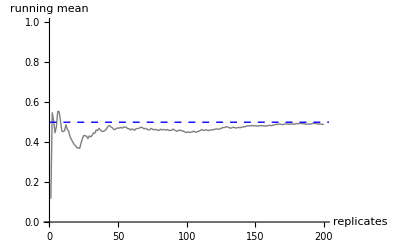

```mathematica
n = 200;
vData=RandomVariate[UniformDistribution[{0,1}],{n}];
vMean=Accumulate[vData]/Table[i,{i,1,n}];
ListLinePlot[vMean,PlotRange->{Automatic,{0,1}},PlotStyle->Gray,Epilog->{Dashed,Blue,Line[{{0,0.5},{1000,0.5}}]},BaseStyle->{FontSize->16},AxesLabel->{"replicates ","running  mean "}]
```